```mathematica
(* Evaporative flux for different mulch thickness *)
```

```mathematica
colors={Red,White,Green,White,Cyan,White};
(* Fine soil data *)
FSdata={Around[30.00,2.085038438],0,Around[10.62,0.204741981],0, Around[4.97,0.2],0};
(* Coarse soil data *)
CSdata={Around[22.8,1.692368723],0,Around[8.432803188,0.952999281],0, Around[6.814120392,1.123055292]};
```

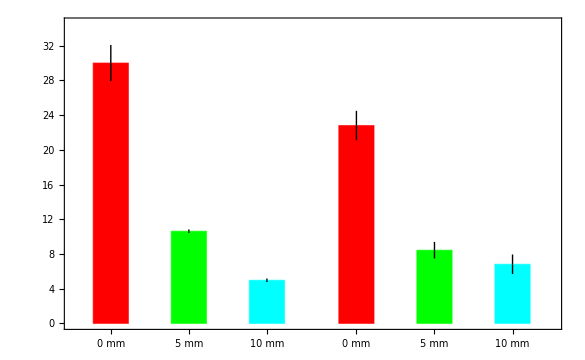

```mathematica
(* Left side for Fine soil, Right side for Coarse soil *)
BarChart[{FSdata,CSdata},ChartLabels->{"0 mm"," ","5 mm"," ","10 mm"," "},ChartStyle->colors,AspectRatio->8/13,ImageSize->{13,8}*45,Frame->True,PlotRange->{{0.25,12.5},{0,34.5}},FrameStyle->Directive[{24,Black,Thickness[0.00275]}]]
```

```mathematica
(* Evaporative flux for different water table *)
```

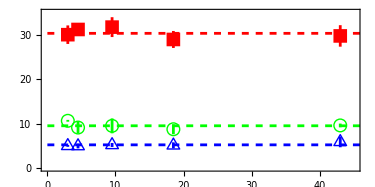

```mathematica
colors={Red,Green,Blue};
(* Fine soil data *)
FS00={{3,30.00,2.085038438},{4.5,31.17,1.434344666},{9.5,31.70,2.232617176},{18.5,28.92266667,1.909523002},{43,29.72,2.418434571}};
FS05={{3, 10.62, 0.204741981},{4.5, 9.10 ,1.35096792},{9.5 ,9.48 ,1.675966686},{18.5, 8.72 ,1.117884908},{43, 9.58 ,0.410645686}};
FS10={{3, 4.97 ,0.2},{4.5 ,4.93 ,0.516294934},{9.5, 5.18 ,0.447743989},{18.5, 5.09475, 0.678751489},{43, 5.87 ,1.203684237}};
plotFSflux=Show[{
(* data points *)
ListPlot[Table[{FS00[[i,1]],FS00[[i,2]]},{i,1,Length[FS00]}],Joined->False,PlotStyle->{Dashed,colors[[1]]},PlotMarkers->{"■",14}],
ListPlot[Table[{FS05[[i,1]],FS05[[i,2]]},{i,1,Length[FS05]}],Joined->False,PlotStyle->{Dashed,colors[[2]]},PlotMarkers->{"○",13}],
ListPlot[Table[{FS10[[i,1]],FS10[[i,2]]},{i,1,Length[FS10]}],Joined->False,PlotStyle->{Dashed,colors[[3]]},PlotMarkers->{"△",15}],
(* error bars *)
ListPlot[Table[{{FS00[[i,1]],FS00[[i,2]]-FS00[[i,3]]},{FS00[[i,1]],FS00[[i,2]]+FS00[[i,3]]}},{i,1,Length[FS00]}],Joined->True,PlotStyle->colors[[1]]],
ListPlot[Table[{{FS05[[i,1]],FS05[[i,2]]-FS05[[i,3]]},{FS05[[i,1]],FS05[[i,2]]+FS05[[i,3]]}},{i,1,Length[FS05]}],Joined->True,PlotStyle->colors[[2]]],
ListPlot[Table[{{FS10[[i,1]],FS10[[i,2]]-FS10[[i,3]]},{FS10[[i,1]],FS10[[i,2]]+FS10[[i,3]]}},{i,1,Length[FS10]}],Joined->True,PlotStyle->colors[[3]]],
(*mean*)
Plot[{Mean[Table[FS00[[i,2]],{i,1,Length[FS00]}]],Mean[Table[FS05[[i,2]],{i,1,Length[FS05]}]],
Mean[Table[FS10[[i,2]],{i,1,Length[FS10]}]]},{x,0,85},PlotStyle->Table[{Dashed,colors[[i]]},{i,1,3}]]
},PlotRange->{{0,45},{0,35}},Frame->True,PlotRange->{{0,45},{0,35}},AspectRatio->1.5/3,ImageSize->{375,200},FrameStyle->Directive[{15,Black,Thickness[0.00275]}],AxesOrigin->{0,0}]
```

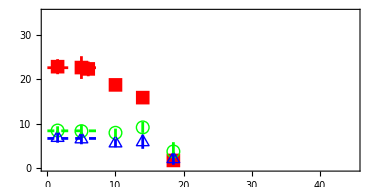

```mathematica
(* Coarse soil data *)
CS00={{1.5, 22.8, 1.692368723},{5 ,22.6 ,2.56},{6 ,22.3 ,1.655665703},{10 ,18.7 ,0.935776814},{14, 15.83550764 ,0.032173191},{18.5, 1.7,0}};
CS05={{1.5 ,8.432803188 ,0.952999281},{5 ,8.294272084, 1.373242726},{10 ,7.924590886 ,0.93612619},{14, 9.132759353 ,1.23586792},{18.5 ,3.72 ,2.09}};
CS10={{1.5, 6.814120392, 1.123055292},{5, 6.486910315, 1.14901281},{10, 5.574764303 ,0.915018004},{14 ,5.84271247 ,1.526689857},{18.5 ,2.03 ,1.29}};
plotCSflux=Show[{
(* data points *)
ListPlot[Table[{CS00[[i,1]],CS00[[i,2]]},{i,1,Length[CS00]}],Joined->False,PlotStyle->{Dashed,colors[[1]]},PlotMarkers->{"■",14}],
ListPlot[Table[{CS05[[i,1]],CS05[[i,2]]},{i,1,Length[CS05]}],Joined->False,PlotStyle->{Dashed,colors[[2]]},PlotMarkers->{"○",13}],
ListPlot[Table[{CS10[[i,1]],CS10[[i,2]]},{i,1,Length[CS10]}],Joined->False,PlotStyle->{Dashed,colors[[3]]},PlotMarkers->{"△",15}],
(* error bars *)
ListPlot[Table[{{CS00[[i,1]],CS00[[i,2]]-CS00[[i,3]]},{CS00[[i,1]],CS00[[i,2]]+CS00[[i,3]]}},{i,1,Length[CS00]}],Joined->True,PlotStyle->colors[[1]]],
ListPlot[Table[{{CS05[[i,1]],CS05[[i,2]]-CS05[[i,3]]},{CS05[[i,1]],CS05[[i,2]]+CS05[[i,3]]}},{i,1,Length[CS05]}],Joined->True,PlotStyle->colors[[2]]],
ListPlot[Table[{{CS10[[i,1]],CS10[[i,2]]-CS10[[i,3]]},{CS10[[i,1]],CS10[[i,2]]+CS10[[i,3]]}},{i,1,Length[CS10]}],Joined->True,PlotStyle->colors[[3]]],
(*mean*)
Plot[{Mean[Table[CS00[[i,2]],{i,1,3}]],Mean[Table[CS05[[i,2]],{i,1,2}]],
Mean[Table[CS10[[i,2]],{i,1,2}]]},{x,0,8},PlotStyle->Table[{Dashed,colors[[i]]},{i,1,3}]]
},PlotRange->{{0,45},{0,35}},Frame->True,PlotRange->{{0,45},{0,35}},AspectRatio->1.5/3,ImageSize->{375,200},FrameStyle->Directive[{15,Black,Thickness[0.00275]}],AxesOrigin->{0,0}]
```

```mathematica
(* Volume of water in reservoir as function of time *)
```

```mathematica
evapvstime=Import[StringJoin[NotebookDirectory[],"/fine_soil_log.dat"]];
colors={{Thickness[0.004],Red,Dashed},{Thickness[0.003],Green,Dashed},{Thickness[0.003],Blue,Dashed}};
fs=ListPlot[{
Table[{evapvstime[[i,1]],V0-evapvstime[[i,2]]},{i,1,Length[evapvstime]}],
Table[{evapvstime[[i,1]],V0-evapvstime[[i,3]]},{i,1,Length[evapvstime]}],
Table[{evapvstime[[i,1]],V0-evapvstime[[i,4]]},{i,1,Length[evapvstime]}]
},Joined->True,PlotStyle->colors,PlotRange->{{0,125},{3,26}},Frame->True,AspectRatio->8/13,ImageSize->{13,8}*40,FrameStyle->Directive[{20,Black,Thickness[0.00275]}],AxesOrigin->{0,0}];
```

```mathematica
evapvstime=Import[StringJoin[NotebookDirectory[],"/coarse_soil_log.dat"]];
colors={{Thickness[0.005],Red},{Thickness[0.004],Green},{Thickness[0.004],Blue}};
cs=ListPlot[{
Table[{evapvstime[[i,1]],V0-evapvstime[[i,2]]},{i,1,Length[evapvstime]}],
Table[{evapvstime[[i,1]],V0-evapvstime[[i,3]]},{i,1,Length[evapvstime]}],
Table[{evapvstime[[i,1]],V0-evapvstime[[i,4]]},{i,1,Length[evapvstime]}]
},Joined->True,PlotStyle->colors,PlotRange->{{0,125},{3,26}},Frame->True,AspectRatio->8/13,ImageSize->{13,8}*40,FrameStyle->Directive[{20,Black,Thickness[0.00275]}],AxesOrigin->{0,0}];
```

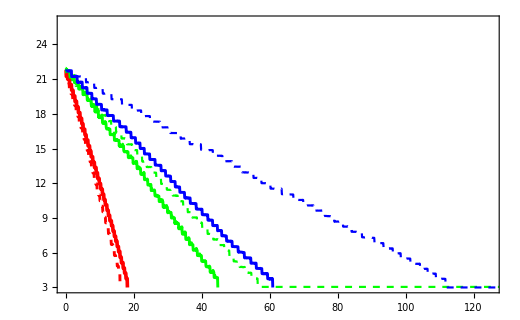

```mathematica
Show[{fs,cs}]
```

```mathematica
(* Soil column temperature profile comparisons between experiment and simulation *)
```

```mathematica
(* Fine soil *)
ENfs1=Table[{tempFS00[[i,1]],(tempFS00[[i,2]]-nlmFS00[[1]])/(nlmFS00[[2]]/.z->0)},{i,1,4}];
ENfs2=Table[{tempFS05[[i,1]],(tempFS05[[i,2]]-nlmFS05[[1]])/(nlmFS05[[2]]/.z->0)},{i,1,4}];
ENfs3=Table[{tempFS10[[i,1]],(tempFS10[[i,2]]-nlmFS10[[1]])/(nlmFS10[[2]]/.z->0)},{i,1,4}];

dfs1=Flatten[Import[StringJoin[NotebookDirectory[],"/fs00_Tprofile_t48hrs.dat"]]];
dfs2=Flatten[Import[StringJoin[NotebookDirectory[],"/fs05_Tprofile_t48hrs.dat"]]];
dfs3=Flatten[Import[StringJoin[NotebookDirectory[],"/fs10_Tprofile_t48hrs.dat"]]];
dataSimFS1=Table[{-(i-1)/10,dfs1[[i]]},{i,1,Length[dfs1]}];
dataSimFS2=Table[{-(i-1)/10,dfs2[[i]]},{i,1,Length[dfs2]}];
dataSimFS3=Table[{-(i-1)/10,dfs3[[i]]},{i,1,Length[dfs3]}];
SNfs1=Table[{dataSimFS1[[i,1]],(dataSimFS1[[i,2]]-20)/(dataSimFS1[[1,2]]-20)},{i,1,Length[dataSimFS1]}];
SNfs2=Table[{dataSimFS2[[i,1]],(dataSimFS2[[i,2]]-20)/(dataSimFS2[[1,2]]-20)},{i,1,Length[dataSimFS2]}];
SNfs3=Table[{dataSimFS3[[i,1]],(dataSimFS3[[i,2]]-20)/(dataSimFS3[[1,2]]-20)},{i,1,Length[dataSimFS3]}];

Show[{
ListPlot[{SNfs1,SNfs2,SNfs3},PlotStyle->{Red,{Dotted,Green},{Dashed,Blue}},Joined->True,Frame->True,PlotRange->{{-45,0.01},{-0.1,1.25}},AspectRatio->1.5/3,ImageSize->{375,200},FrameStyle->Directive[{15,Black,Thickness[0.003]}],GridLines->{{},{0}},GridLinesStyle->Directive[Black, Dashed]],
ListPlot[{ENfs1,ENfs2,ENfs3},PlotStyle->{Red,Green,Blue},PlotMarkers->{{"□",15},{"○",13},{"×",20}},Frame->True,PlotRange->{{-45,0.01},{-0.1,1.25}},AspectRatio->1.5/3,ImageSize->{375,200},FrameStyle->Directive[{15,Black,Thickness[0.003]}]]
}]
```

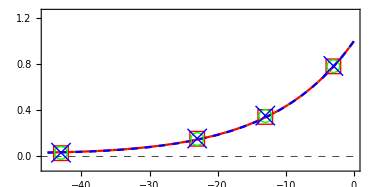

```mathematica
(* Coarse soil *)
```

```mathematica
ENcs1=Table[{tempCS00[[i,1]],(tempCS00[[i,2]]-nlmCS00[[1]])/(nlmCS00[[2]]/.z->0)},{i,1,4}];
ENcs2=Table[{tempCS05[[i,1]],(tempCS05[[i,2]]-nlmCS05[[1]])/(nlmCS05[[2]]/.z->0)},{i,1,4}];
ENcs3=Table[{tempCS10[[i,1]],(tempCS10[[i,2]]-nlmCS10[[1]])/(nlmCS10[[2]]/.z->0)},{i,1,4}];

dcs1=Flatten[Import[StringJoin[NotebookDirectory[],"/cs00_Tprofile_t48hrs.dat"]]];
dcs2=Flatten[Import[StringJoin[NotebookDirectory[],"/cs05_Tprofile_t48hrs.dat"]]];
dcs3=Flatten[Import[StringJoin[NotebookDirectory[],"/cs10_Tprofile_t48hrs.dat"]]];
dataSimCS1=Table[{-(i-1)/10,dcs1[[i]]},{i,1,Length[dcs1]}];
dataSimCS2=Table[{-(i-1)/10,dcs2[[i]]},{i,1,Length[dcs2]}];
dataSimCS3=Table[{-(i-1)/10,dcs3[[i]]},{i,1,Length[dcs3]}];
SNcs1=Table[{dataSimCS1[[i,1]],(dataSimCS1[[i,2]]-20)/(dataSimCS1[[1,2]]-20)},{i,1,Length[dataSimCS1]}];
SNcs2=Table[{dataSimCS2[[i,1]],(dataSimCS2[[i,2]]-20)/(dataSimCS2[[1,2]]-20)},{i,1,Length[dataSimCS2]}];
SNcs3=Table[{dataSimCS3[[i,1]],(dataSimCS3[[i,2]]-20)/(dataSimCS3[[1,2]]-20)},{i,1,Length[dataSimCS3]}];

Show[{
ListPlot[{SNcs1,SNcs2,SNcs3},PlotStyle->{Red,{Dotted,Green},{Dashed,Blue}},Joined->True,Frame->True,PlotRange->{{-45,0.01},{-0.1,1.25}},AspectRatio->1.5/3,ImageSize->{375,200},FrameStyle->Directive[{15,Black,Thickness[0.003]}],GridLines->{{},{0}},GridLinesStyle->Directive[Black, Dashed]],
ListPlot[{ENcs1,ENcs2,ENcs3},PlotStyle->{Red,Green,Blue},PlotMarkers->{{"□",15},{"○",13},{"×",20}},Frame->True,PlotRange->{{-45,0.01},{-0.1,1.25}},AspectRatio->1.5/3,ImageSize->{375,200},FrameStyle->Directive[{15,Black,Thickness[0.003]}]]
}]
```

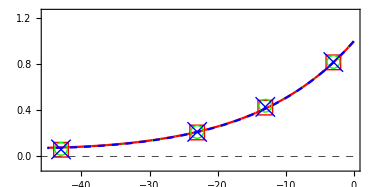

```mathematica
(* Surface temperature comparisonsbetween experiment and simulation *)
```

```mathematica
(* Simulation data {mulch thickness (mm), top mulch temperature (deg C)} *)
(* Coarse soil *)
cstopT={{3,38.33285770892601},{5,41.66421311420479},{8,44.39678369951665},{10,45.578193396523474},{13,46.87726575653538},{15,47.547813849976166},{18,48.36641678612268},{20,48.82226987341075}};
fstopT={{3,39.23099129375874},{5,42.77820574740434},{8,45.656764547094916},{10,46.874007298659805},{13,48.177822331762286},{15,48.83169917829048},{18,49.6081352679029},{20,50.028844596009925}};
```

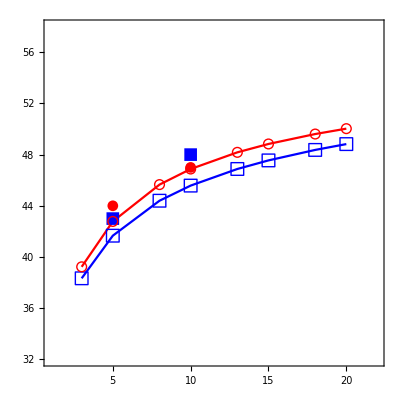

```mathematica
ListPlot[{cstopT,fstopT,{{5,43},{10,48}},{{5,44},{10,47}}}(* Experimental data *),Joined->{True,True,False,False},PlotStyle->{Blue,Red},PlotMarkers->{{"□",13},{"○",10},{"■",13},{"●",11}},Frame->True,AspectRatio->1,ImageSize->{400,400},PlotRange->{{1,22},{32,58}},FrameStyle->Directive[{15,Black,Thickness[0.003]}]]
```

```mathematica
(* Evaporative flux (mm/day) as function of surface temperature (deg C)*)
```

```mathematica
(* Experimental data *)
(* Coarse soil *)
EXPTopSoilTempVSFluxSS={ 
{35.7,22.06},
{36.7,23},
{37,25},
{38.14,26.25},
{45.39,39.56},
{46.98,42.69},
{55.24,62}
};
(* Fine soil *)
EXPTopSoilTempVSFluxFS={
{38,25.47},
{40,31.44},
{40.4,32.73},
{41.12,34.75},
{50.85,50.93},
{58.71,62.73}
};
databare=Join[EXPTopSoilTempVSFluxSS,EXPTopSoilTempVSFluxFS];
```

```mathematica
model3=Normal[NonlinearModelFit[databare,N[ae/(√R)(Pv[TT]/(√(273.15+TT))-1.280/(√(273.15+Tinv)))1000/10^6×10^6((24×60×60)/(10^-3×1000))],{ae},TT]];
```

0.00120472

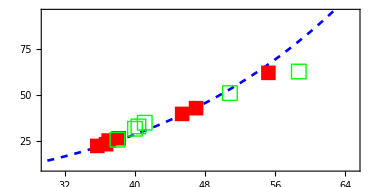

```mathematica
σa=0.0628360214683037;(*accomodation parameter*)
Tinv=20;
R=461.52;(*J/kg K gas constant*)
αe=N[(2σa)/(2-σa)(2π R)^(-1/2)]
Pv[T_]:=0.61078Exp[(17.27T)/(T+237.3)];(*kPa*)
Show[{
Plot[model3,{TT,30,65},PlotStyle->Directive[Blue,Dashed,Thickness[0.005]]],
ListPlot[EXPTopSoilTempVSFluxSS,PlotStyle->Red,PlotMarkers->{"■",15}],
ListPlot[EXPTopSoilTempVSFluxFS,PlotStyle->Green,PlotMarkers->{"□",15}]
},PlotRange->{{30,65},{10,95}},Frame->True,AspectRatio->1.5/3,ImageSize->{375,200},FrameStyle->Directive[{15,Black,Thickness[0.003]}]]
```

```mathematica
(* Evaporative flux as function of mulch thickness, comparison between experiment and simulation value*)
```

```mathematica
(*Simulation data {mulch thickness (mm), evaporative flux (mm/day)}*)
SIMmulchSS={
{5,9.998},
{6,8.51},
{7,7.4},
{8,6.54},
{9,5.85},
{10,5.292},
{11,4.826},
{12,4.432},
{13,4.0945},
{14,3.8},
{15,3.547},
{16,3.32},
{17,3.1212},
{18,2.942},
{19,2.781},
{20,2.6355},
{21,2.50},
{22,2.38},
{23,2.271},
{24,2.17},
{25,2.076}
};

(*Experimental data for Fine soil {mulch thickness (mm), evaporative flux (mm/day), SD}*)
EXPmulchFS={
{5,10.62,0.2},
{10, 4.97, 0.2}
};

(*Experimental data for Coarse soil {mulch thickness (mm), evaporative flux (mm/day), SD}*)
EXPmulchSS={
{5,8.43,0.953},
{10,6.81,1.123},
{15,3.438,0.1494},
{17.5,3.113,1.592},
{20,2.66,0.59397}
};
```

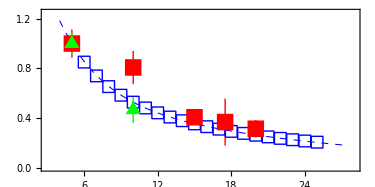

```mathematica
Clear[z,modelfit3]
modelfit3[z_]:=20.0743 ⅇ^(−0.2963z)+6.9036 ⅇ^(−0.04889z);
Show[{
Plot[modelfit3[z]/modelfit3[5],{z,4,27.5},PlotStyle->Directive[Blue,Dashed,Thickness[0.002]],PlotRange->{{3,28},{0,1.25}},Frame->True,AspectRatio->1.5/3,ImageSize->{375,200},FrameStyle->Directive[{15,Black,Thickness[0.003]}]],
ListPlot[{
Table[{SIMmulchSS[[i,1]],SIMmulchSS[[i,2]]/SIMmulchSS[[1,2]]},{i,1,Length[SIMmulchSS]}],
Table[{EXPmulchSS[[i,1]],Around[EXPmulchSS[[i,2]],EXPmulchSS[[i,3]]]/EXPmulchSS[[1,2]]},{i,1,Length[EXPmulchSS]}],
Table[{EXPmulchFS[[i,1]],Around[EXPmulchFS[[i,2]],EXPmulchSS[[i,3]]]/EXPmulchFS[[1,2]]},{i,1,Length[EXPmulchFS]}]
},PlotStyle->{Blue,Red,Green,Purple,Black},PlotMarkers->{{"□",12},{"■",17},{"▲",18},{"▲",15},{"▲",15}}]
}]
```